```mathematica
Clear["Global`*"]
```

```mathematica
elements={{"Lens",6.24,6.24},{"Lens",150,150},{"Lens",300,Infinity},{"Lens",345,45},{"Lens",645,Infinity},{"Lens",1145,30},{"Lens",1175,Infinity}};
(*elements={{"Lens",6.24,6.24},{"Lens",10,150},{"Lens",160,Infinity},{"Lens",205,45},{"Lens",500,100},{"Lens",750,30},{"Lens",780,Infinity}}*)
freespace={};
zmax=5000;
λ=515*10^-6;
inputparms={w0->3/2*10^-3,R0->Infinity};(*input waist and curvature in mm*)
lim = 5;
lensMatrix[f_]:={{1,0},{-1/f,1}}
freeMatrix[d_]:={{1,d},{0,1}}
matrix[optic_]:=If[optic[[1]]=="Lens",lensMatrix[optic[[3]]],IdentityMatrix[2]]

abcd[z_,optics_]:=Module[{},
elem=Sort[Select[optics,#[[2]]≤z &],#1[[2]]>#2[[2]] &];
matrixlist=If[Length[elem]≥1,
Flatten[Join[{{freeMatrix[z-First[elem][[2]]]},Flatten[Table[{matrix[elem[[ii]]],freeMatrix[elem[[ii,2]]-elem[[ii+1,2]]]},{ii,1,Length[elem]-1}],1],{matrix[Last[elem]]},{freeMatrix[Last[elem][[2]]]}}],1],{freeMatrix[z]}];
orderlist=Reverse[matrixlist];
fullMatrix=IdentityMatrix[2];
For[ii=1,ii≤Length[orderlist],ii++,
fullMatrix=orderlist[[ii]].fullMatrix];
fullMatrix
]
q0recip=1/R0-ⅈ λ/(π w0^2)/.inputparms;
z0=(π w0^2)/λ/.inputparms;
qrecip[z_,optics_]:=(abcd[z,optics][[2,1]]+abcd[z,optics][[2,2]]*q0recip)/(abcd[z,optics][[1,1]]+abcd[z,optics][[1,2]]*q0recip)
rcurv[z_,optics_]:=(Re[qrecip[z,optics]])^-1
waist[z_,optics_]:=(-(Im[qrecip[z,optics]]*π)/λ)^(-1/2)
```

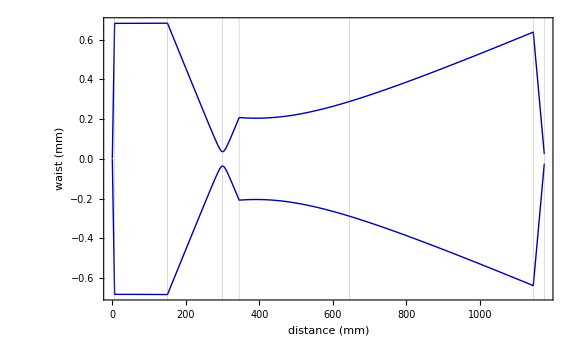

```mathematica
Plot[{waist[z,elements],-waist[z,elements]},{z,0,elements[[-1,2]]},PlotStyle->{{Thick,Darker[Blue]},{Thick,Darker[Blue]}},Frame->True, GridLines->{elements[[All,2]],{}},ImageSize->Large,FrameLabel->{"distance (mm)","waist (mm)"}, PlotRange-> All]
```

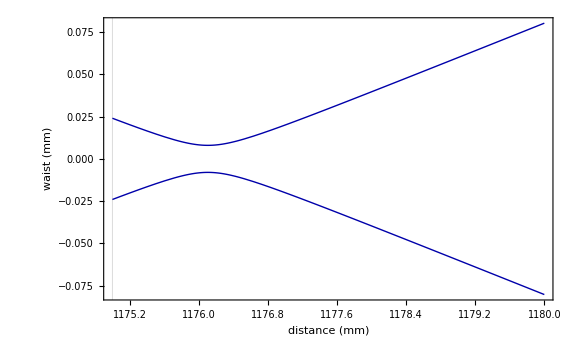

```mathematica
Plot[{waist[z,elements],-waist[z,elements]},{z,1175,1180},PlotStyle->{{Thick,Darker[Blue]},{Thick,Darker[Blue]}},Frame->True, GridLines->{elements[[All,2]],{}},ImageSize->Large,FrameLabel->{"distance (mm)","waist (mm)"}, PlotRange-> All]
```

```mathematica
wGal=waist[elements[[-4,2]],elements]//N
zr=(π w0^2)/λ
wColl = waist[elements[[-2,2]],elements]//N
wAtom = waist[elements[[-1,2]],elements]//N
```

0.0360577

7.93119

0.206639

0.0240385

```mathematica
1/(wGal/10)
1/(wColl/10)
```

277.333

48.3936

```mathematica
(.5)/((100*10^-4)^2)
```

5000.